## 4 level atoms

#### Code Parameters

```mathematica
IntPic=1; (* Use interaction picture: Yes or No? *)
tf = 1; (* Final time *)
measure=1; (* Measurements/ make the atoms interact with N,N photons during the measurement phase: Yes or No? *)
ShineFullTime =0; (* Make the atoms interact with N,N photons all the time.: Yes or No? *)
add=0; (* Photon addition during meaasurement? No. Set to 0. We must have N photon states already prepared *)
fraction=10/100;(* Subscript[τ, m]/τ  ---- Ideallly this should go to zero *)
coupling=2 ; (* Ω *)
interval = 2 10^-1;(* Interval size that gives Half-Rabi flop is approximately 1/fraction π/(2coupling √(phots+1/2));*)
totstps =IntegerPart[tf/interval]; (* Total number of time steps  *)
phots=IntegerPart[(1/(fraction interval)π/(2coupling))^2-1/2];

τplusτm=(measure,0 totstps+measure,1)  interval ;   (* Actual interval sizes between the measurements *)
τm =(measure,0 ShineFullTime,1+measure,1 fraction)τplusτm; (* Duration of the measurement ---- ideally this should be vanishingly small *)
NumberOfSubspaces=2; (* Number of exicted-ground level pairs *)
M=2;(* Number of atoms *)
Delta =5; (* Some parameter to decide frequency shifts *)

(* Plotting parameters *)
thick = 0.002; (* Plot thickness *)
pltmin =1-0.0165;(*1-0.016;*)
pltmax=1;(*0+0.016;*)
```

#### Constructing Hilbert Space

```mathematica
cons[Atom_,Subspace_,N1_]:=Module[{a},
a=ConstantArray[Subspace,M+2];
a[[Atom]]=NumberOfSubspaces+Subspace;
a[[M+1]]=N1;
a[[M+2]]=N1;
a ];

For[m=1,m<=M,m++,

(* Subspace I *)
ψI[m]= cons[m,1,N1];

(* Subspace II *)
ψII[m]= cons[m,2,N1];
];
ClearAll[m];

NextStatesI[KnownStates_,BoundaryStates_]:=
Module[
{a,b,NextKnown,NextBoundary},
b={};
Do[(* Go through all the boundary states *)

Do[(* Check the states of all the atoms one by one *)

(* Subscript[E, 1] can change to Subscript[G, 1] *)
a =BoundaryStates[[m]];
If[
a[[k]]==NumberOfSubspaces+1,
a[[k]]=1;  
a[[M+1]]= a[[M+1]]+1;
b=Append[b,a];
];
(* Subscript[E, 2] can change to Subscript[G, 2] *)
a =BoundaryStates[[m]];
If[
a[[k]]==NumberOfSubspaces+2,
a[[k]]=2;  
a[[M+2]]= a[[M+2]]+1;
b=Append[b,a];
];
(* Subscript[G, 1] can change to Subscript[E, 1] only *)
a =BoundaryStates[[m]];
If[a[[k]]==1,
a[[k]]=NumberOfSubspaces+1;
a[[M+1]]= a[[M+1]]-1;
b=Append[b,a]];
(* Subscript[G, 2] can change to Subscript[E, 2] only *)
If[a[[k]] =2,
a[[k]]=NumberOfSubspaces+2;  
a[[M+2]]= a[[M+2]]-1;
b=Append[b,a];
]

,{k,1,M}];

,{m,1,Dimensions[BoundaryStates][[1]]}];

b= DeleteDuplicates[b]; (* These are the all the possible next boundary states if they are not already known *)

NextKnown =KnownStates~Join~b;
NextKnown = DeleteDuplicates[NextKnown];

If[Dimensions[NextKnown][[1]]>Dimensions[KnownStates][[1]],
NextBoundary = NextKnown[[Dimensions[KnownStates][[1]]+1;;]]
,NextBoundary={}
];
{NextKnown,NextBoundary}

];

NextStatesII[KnownStates_,BoundaryStates_]:=
Module[
{a,b,NextKnown,NextBoundary},
b={};
Do[(* Go through all the boundary states *)

Do[(* Check the states of all the atoms one by one *)

(* Subscript[E, 2] can change to Subscript[G, 2] *)
a =BoundaryStates[[m]];
If[
a[[k]]==NumberOfSubspaces+2,
a[[k]]=2;  
a[[M+2]]= a[[M+2]]+1;
b=Append[b,a];
];
(* Subscript[E, 1] can change to Subscript[G, 1] *)
a =BoundaryStates[[m]];
If[
a[[k]]==NumberOfSubspaces+1,
a[[k]]=1;  
a[[M+1]]= a[[M+1]]+1;
b=Append[b,a];
];
(* Subscript[G, 2] can change to Subscript[E, 2] only *)
a =BoundaryStates[[m]];
If[a[[k]]==2,
a[[k]]=NumberOfSubspaces+2;
a[[M+2]]= a[[M+2]]-1;
b=Append[b,a]];
(* Subscript[G, 1] can change to Subscript[E, 1] only *)
If[a[[k]] =1,
a[[k]]=NumberOfSubspaces+1;  
a[[M+1]]= a[[M+1]]-1;
b=Append[b,a];
]

,{k,1,M}];

,{m,1,Dimensions[BoundaryStates][[1]]}];

b= DeleteDuplicates[b]; (* These are the all the possible next boundary states if they are not already known *)

NextKnown =KnownStates~Join~b;
NextKnown = DeleteDuplicates[NextKnown];

If[Dimensions[NextKnown][[1]]>Dimensions[KnownStates][[1]],
NextBoundary = NextKnown[[Dimensions[KnownStates][[1]]+1;;]]
,NextBoundary={}
];
{NextKnown,NextBoundary}

];

InitialStatesI=ψI[#]&/@Range[M];
BoundaryI = InitialStatesI;
KnownI = InitialStatesI;
InitialStatesII=ψII[#]&/@Range[M];
BoundaryII = InitialStatesII;
KnownII = InitialStatesII;

OI=0;
For[{tmpk,tmpb} ={ InitialStatesI, InitialStatesI},BoundaryI!={},{KnownI,BoundaryI}={tmpk,tmpb},
OI=OI+1;
{tmpk, tmpb}= NextStatesI[KnownI,BoundaryI];
(*Print[OI];
Print[MatrixForm[tmpb]];*)
];
{KnownI, BoundaryI}= NextStatesI[KnownI, BoundaryI];
OI=OI-1;
dimKI = Dimensions[KnownI][[1]];


OII=0;
For[{tmpk,tmpb} ={ InitialStatesII, InitialStatesII},BoundaryII!={},{KnownII,BoundaryII}={tmpk,tmpb},
OII=OII+1;
{tmpk, tmpb}= NextStatesII[KnownII,BoundaryII];
(*Print[OII];
Print[MatrixForm[tmpb]];*)
];
{KnownII, BoundaryII}= NextStatesII[KnownII, BoundaryII];
OII=OII-1;
dimKII = Dimensions[KnownII][[1]];

Known = KnownI~Join~KnownII;
dimK = Dimensions[Known][[1]];
(* Known are the states whose span constructs the Hilbert space *)
```

#### Hamiltonian

```mathematica
(* Field only Hamiltonian *)
HfieldMatrixElements[p_,q_] := KroneckerDelta[p,q]( ℏ ω1  (Known[[p,M+1]]+1/2)+ℏ ω2  (Known[[p,M+2]]+1/2));
Hfield = Table[HfieldMatrixElements[p,q],{p,1,Dimensions[Known][[1]]},{q,1,Dimensions[Known][[1]]}];


(* Atoms only Hamiltonian *)
HatomsMatrixElements[p_,q_]:=Module[{a},
a=0;
If[p==q,
Do[
a = a+ℏ KroneckerDelta[Known[[p,m]],1]g1[m]+ℏ KroneckerDelta[Known[[p,m]],2]g2[m]+ℏ KroneckerDelta[Known[[p,m]],NumberOfSubspaces+1]e1[m]+ℏ KroneckerDelta[Known[[p,m]],NumberOfSubspaces+2]e2[m]  ;
,{m,1,M}];
];
a
];
Hatoms = Table[HatomsMatrixElements[p,q],{p,1,Dimensions[Known][[1]]},{q,1,Dimensions[Known][[1]]}];

(* Module that tells if two states are connected by a first-order perturbation ----- this is like an adajacency matrix of a graph but for a state *)
IsEdge[ψ1_,ψ2_]:=Module[{diffNum,diff},

diffNum=0;
diff=0;

For[k=1,k<=M,k++,
If[ψ1[[k]]!=ψ2[[k]],
diffNum++;
diff=diff+ψ1[[k]]-ψ2[[k]]
];
];
diffNum==1&&(Abs[diff]==NumberOfSubspaces)  
&&(
(ψ1[[M+1]]-ψ2[[M+1]]==0)
⊻
(ψ1[[M+2]]-ψ2[[M+2]]==0))
&&
((ψ2[[M+1]]-ψ1[[M+1]])Sign[diff]==1)
⊻
((ψ2[[M+2]]-ψ1[[M+2]])Sign[diff]==1)
];

(* Atom-Field interaction Hamiltonian constructed out of  IsEdge *)
HintMatrixElements[p_,q_]:=Module[{a},
a=0;
If[IsEdge[Known[[p]],Known[[q]]],

Do[
a= a+KroneckerDelta[Abs[Known[[p,m]]  -Known[[q,m]]],NumberOfSubspaces](
ℏ Ωal[m]/2 √( Known[[p,M+1]]   KroneckerDelta[Known[[p,m]],1]   UnitStep[ Known[[p,M+1]] -Known[[q,M+1]]]+      Known[[q,M+1]]KroneckerDelta[Known[[q,m]],1]  UnitStep[ Known[[q,M+1]] -Known[[p,M+1]]] ) +ℏ Ωal[m]/2 √( Known[[p,M+2]] KroneckerDelta[Known[[p,m]],2]  UnitStep[ Known[[p,M+2]] -Known[[q,M+2]] ]  +      Known[[q,M+2]] KroneckerDelta[Known[[q,m]],2]  UnitStep[ Known[[q,M+2]] -Known[[p,M+2]] ]  )
)
,{m,1,M}];
] ;
a
];
Hint = Table[HintMatrixElements[p,q],{p,1,Dimensions[Known][[1]]},{q,1,Dimensions[Known][[1]]}];

(* CASE 1: When the number of photons are N = 0, N= 0 we have a smaller Hilbert space and a smaller Hamiltonian *)
H0[1][N1_] = Hfield+Hatoms;
Hint = MatrixExp[ⅈ KroneckerDelta[IntPic,1] ((t-t0)/ℏ)H0[1][N1]].Hint.MatrixExp[-ⅈ  KroneckerDelta[IntPic,1]((t-t0)/ℏ)H0[1][N1]];
Htot[1][N1_,t0_]=KroneckerDelta[IntPic,0]( H0[1][N1]) + Hint;


(* CASE 2: When the number of photons are N, N as in during the measurement the Hilbert space is larger and Hamiltonian is larger. *)
H0[2] [N1_]= Module[{a},
a=ConstantArray[0,{2(M+1),2(M+1)}];
a[[1;;M+1,1;;M+1]]=H0[1][0] [[1;;M+1,1;;M+1]];
a[[M+2;;2M+2,M+2;;2M+2]]=H0[1][0][[Dimensions[KnownI][[1]]+1;;Dimensions[KnownI][[1]]+M+1,Dimensions[KnownI][[1]]+1;;Dimensions[KnownI][[1]]+M+1]];
a
];

Htot[2][N1_,t0_]= Module[{a},
a=ConstantArray[0,{2(M+1),2(M+1)}];
a[[1;;M+1,1;;M+1]]=Htot[1][0,t0] [[1;;M+1,1;;M+1]];
a[[M+2;;2M+2,M+2;;2M+2]]=Htot[1][0,t0][[Dimensions[KnownI][[1]]+1;;Dimensions[KnownI][[1]]+M+1,Dimensions[KnownI][[1]]+1;;Dimensions[KnownI][[1]]+M+1]];
a
];
```

#### Fock states used during the measurements

```mathematica
N1=phots;
```

#### Main Calculations

```mathematica
ℏ=1;

FrameChange=0; (* Calculations in the photons' rotating frame: Yes or No?  *)
ωph=10^2; (* Photon energy *)
ω=FrameChange,0 ωph; 

(* Energy structure chosen arbitrarily *)
ω1=0.5ω; (* Energy of E1-G1 transition. Ideally *)
ω2=1.5ω; (* Energy of E2-G2 transition. Ideally *)
e10 = ω1;
g10=0;
g20= 3e10;
e20= ω2 +g20;


ClearAll[e1,g1,e2,g2];
Do[
rand1 = RandomReal[{-1,1}] ;
rand2= RandomReal[{-1,1}] ;
rand3= RandomReal[{-1,1}] ;
rand4=RandomReal[{-1,1}];
e1[m]=e10+Delta rand1;
g1[m]=g10+Delta rand2;
e2[m]=e20+Delta rand3;
g2[m]=g20+Delta rand4;
Ωal[m]=coupling;

,{m,1,M}];

(* Energy levels of the two atoms after some random frequency shifts *)
e1[1] = 52.0306; 
g1[1] = -4.456930873804201; 
e2[1] = 300.734; 
g2[1] = 149.151; 
e1[2] = 46.375; 
g1[2] = 1.43154; 
e2[2] = 297.901; 
g2[2] = 148.681; 

(* Energy differences *)
e1[1]-g1[1]-ω1
e1[2]-g1[2]-ω1
e2[1]-g2[1]-ω2
e2[2]-g2[2]-ω2

δ1=((e1[1]-g1[1]-ω1)+(e1[2]-g1[2]-ω1))/2
δ2=((e2[1]-g2[1]-ω2)+(e2[2]-g2[2]-ω2))/2
Δ1=(-(e1[1]-g1[1]-ω1)+(e1[2]-g1[2]-ω1))/2
Δ2=(-(e2[1]-g2[1]-ω2)+(e2[2]-g2[2]-ω2))/2
```

6.48753

-5.05654

1.583

-0.78

0.715495

0.4015

-5.77204

-1.1815

```mathematica
size=0;(* determines StepSize of NDSolve *)

tlim=1;(* number of measurement intervals one "step"/ loop of the code *)
totalsteps= measure,0+measure,1 totstps ; (* Total number of "steps"/ loops in the code *)


(* Functions to make plots at each "step"/ loop of the code *)

(* Plots the probabilities *)
pltP={};plotP[step_]:=Plot[{(*TotalProbability[t],*)(*SuccessProbability[t],*)Pemission[t],Psup[t],Psub[t]},{t,tlim τplusτm(step-1),tlim τplusτm(step-1)+tlim τplusτm},AxesLabel->{"t","P"},LabelStyle->Large,ImageSize->Large,PlotRange->{0,1}(*{pltmin,pltmax}*),PlotLegends->If[step==1,{(*"Total",*)(*"Success",*)"em./abs.","super","sub"},None],(*Frame->{{True,False},{True,True}},*)PlotStyle->{{Black, Thick},{Blue,Thick},{Red,Thick}}];

(* Plots the phase drift/ "asynchronicity" *)
pltAsync={};plotAsync[step_]:=Plot[Mod[ϕClockA[t]-ϕClockB[t],2π],{t,tlim τplusτm(step-1),tlim τplusτm(step-1)+tlim τplusτm},AxesLabel->{"t","ϕ_A-ϕ_B"},LabelStyle->Large,ImageSize->Large,PlotRange->{0,2π},(*Frame->{{True,False},{True,True}},*)Ticks->{Automatic,{0,π/2,π,3 π/2,2π}},PlotStyle->{Thick,Black}];
(*
(* Plots Clock phases *)
pltClockPhases={};plotClockPhases[step_]:=Plot[{Mod[ ϕClockA[t],2π],Mod[ϕClockB[t],2π]},{t,tlim τplusτm(step-1),tlim τplusτm(step-1)+tlim τplusτm},AxesLabel->{"t","Phase of the clocks"},LabelStyle->Large,ImageSize->Large,PlotRange->{0,2π},PlotLegends->If[step==1,{"ϕ(Clock A)","ϕ(Clock B)"},None]];

pltPClock={};plotPClock[step_]:=Plot[{PAlice[t],PBob[t]},{t,tlim τplusτm(step-1),tlim τplusτm(step-1)+tlim τplusτm},LabelStyle->Large,ImageSize->Large,PlotStyle-> {{Solid,Blue,Thickness[thick]},{Red,Dashed,Thickness[thick]}},PlotRange->All,PlotLegends->If[step==1,{"P_Alice(+)","P_Bob(+)"},None](*,Axes->None*),Ticks->{None,{0,1}},AxesLabel->{t,P},AxesOrigin->{0,0}];
*)

(* Converting a vector valued 'Interpolating Function' Mathematica object to a vector of scalar valued 'Interpolating function' Mathematica objects *)
IFvectorTovectorIF[IFvector_]:=Module[{vectorIF=ConstantArray[0,IFvector["OutputDimensions"][[1]]]},
For[k=1,k<=IFvector["OutputDimensions"][[1]],k++,
vectorIF[[k]]=Transpose[Append[IFvector["Coordinates"],IFvector["ValuesOnGrid"][[All,k]]]];
vectorIF[[k]]=Interpolation[vectorIF[[k]],InterpolationOrder->IFvector["InterpolationOrder"][[1]],Method->IFvector["InterpolationMethod"]][t]
];
vectorIF
];


(* Initial state *)
X0=ConstantArray[0,2(M+1)];
X0[[1;;M]]=ⅇ^(ⅈ 2 π/M(#-1))&/@Range[M];
X0[[M+2;;2M+1]]=ⅇ^(ⅈ 2 π/M(#-1))&/@Range[M];

X0=X0/Norm[X0];
Print["Initial state: ",X0]

HBefore[t0_]=Htot[2][0,t0];
HAfter[t0_] = Htot[1][N1,t0];

Quiet[Monitor[
Do[
TotalSections=8;
Section=1;
	(* Schrodinger equation *)
Do[
(* Inside n^th measurement interval *)
t0=tlim τplusτm(step-1)+(n-1) τplusτm;
tf=tlim τplusτm(step-1)+n τplusτm -τm;
solBefore[n]=NDSolveValue[{xBefore[n]'[t]==-ⅈ/ℏ HBefore[t0].xBefore[n][t],xBefore[n][t0]==X0},xBefore[n],{t,t0,tf}(*,MaxStepSize->10^-size*)];

Section = 2;
(* Make the atoms interact with N1, N2 photons into the field modes *)
totalProbVariableBefore[n]=0;(* To check if the total probability remains ~ 1*)
ProbAddVariable[n]=0;
ProbSuccessVariableBefore[n]=0;(*To check if the probability of success doesn't drop too much*)
ProbSuccessVariableBefore[0]=1;(*at t=0 there is n1, n2 = 0 photons in two light channels*)

xBefore[n][t_]= ⅇ^(-ⅈ IntPic ((t-t0)/ℏ)ℏ ω(phots+1/2))MatrixExp[-ⅈ  IntPic((t-t0)/ℏ)H0[2][0]].IFvectorTovectorIF[solBefore[n]];
PBefore[n][t_]=Abs[xBefore[n][t]]^2;

totalProbVariableBefore[n]=Total[PBefore[n][t]];
ProbSuccessVariableBefore[n]=Total[PBefore[n][t][[1;;M]]]+Total[PBefore[n][t][[M+2;;2M+1]]];(* Probability of no emission in both the channels *)


Section =3;
(* Schrodinger equation after photon addition *)
X0=ConstantArray[0,dimK];
X0[[1;;M]]=xBefore[n][tf][[1;;M]];
X0[[dimKI+1;;dimKI+M]]=xBefore[n][tf][[M+2;;2M+1]];
X0[[M+1]]=add xBefore[n][tf][[M+1]];
X0[[dimKI+M+1]]=add xBefore[n][tf][[2(M+1)]];
(*X0=X0/Norm[X0];*)

pem=PBefore[n][t][[M+1]];

t0=tf;
tf=tlim τplusτm(step-1)+n τplusτm ;
solAfter[n]=NDSolveValue[{xAfter[n]'[t]==-ⅈ/ℏ HAfter[t0].xAfter[n][t],xAfter[n][t0]==X0},xAfter[n],{t,t0,tf },MaxStepSize->10^-size];

Section=4;
totalProbVariableAfter[n]=0;(*To check if the total probability remains = 1*)
ProbSuccessVariableAfter[n]=0;(*To check if the probability of success doesn't drop too much*)
ProbSuccessVariableAfter[0]=1;(*at t=0 there is n = ph0 photons in light*)

xAfter[n][t_]= MatrixExp[-ⅈ  IntPic((t-t0)/ℏ)H0[1][N1]].IFvectorTovectorIF[solAfter[n]];
PAfter[n][t_]=Abs[xAfter[n][t]]^2;
totalProbVariableAfter[n]=Total[PAfter[n][t]];
ProbSuccessVariableAfter[n]= Total[PAfter[n][t][[1;;M]]]+Total[PAfter[n][t][[dimKI+1;;dimKI+M]]];
PSuccessAfter[t_]=ProbSuccessVariableAfter[n];(*After a successful measurement, the extra N1, N2 photons are subtracted out. We don't get any factors corresponding to this subtraction out in the front as this is a reset step and we renormalize*)

Section=5;
(* Measurement of exactly N1, N2 photons in the field (not more, not less)
	Then, resetting the field to vacuum to ready it for the next measurement interval*)
X0=ConstantArray[0,2(M+1)];
X0[[1;;M]]=xAfter[n][tf][[1;;M]];
X0[[M+2;;2M+1]]=xAfter[n][tf][[dimKI+1;;dimKI+M]];
(*X0=X0/Norm[X0];*)

,{n,1,tlim}];

Section =6;
TotalProbability[t_]=∑_(n=1)^tlim totalProbVariableBefore[n](UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])+∑_(n=1)^tlim totalProbVariableAfter[n](UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]);

SuccessProbability[t_]=∑_(n=1)^tlim ProbSuccessVariableBefore[n](UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])+∑_(n=1)^tlim ProbSuccessVariableAfter[n](UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]);

Pemission[t_]=∑_(n=1)^tlim (PBefore[n][t][[M+1]]+PBefore[n][t][[2(M+1)]])(UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])+∑_(n=1)^tlim (Total[PAfter[n][t][[M+1;;dimKI]]]+Total[PAfter[n][t][[dimKI+M+1;;]]])(UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]);


Psup[t_]=∑_(n=1)^tlim (1/(2M)(Abs[Abs[Total[xBefore[n][t][[1;;M]]]]+Abs[Total[xBefore[n][t][[M+2;;2M+1]]]]]^2))(UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])+∑_(n=1)^tlim (1/(2M)(Abs[Abs[Total[xAfter[n][t][[1;;M]]]]+Abs[Total[xAfter[n][t][[dimKI+1;;dimKI+M]]]]]^2))(UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]);

Psub[t_]=∑_(n=1)^tlim (1/(2M)(Abs[Abs[Total[ⅇ^(-ⅈ 2 π/M(#-1)) xBefore[n][t][[#]]&/@Range[M]]]+Abs[Total[ⅇ^(-ⅈ 2 π/M(#-1)) xBefore[n][t][[M+1+#]]&/@Range[M]]]]^2))(UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])+∑_(n=1)^tlim (1/(2M)(Abs[Abs[Total[ⅇ^(-ⅈ 2 π/M(#-1))xAfter[n][t][[#]]&/@Range[M]]]+Abs[Total[ⅇ^(-ⅈ 2 π/M(#-1))xAfter[n][t][[dimKI+#]]&/@Range[M]]]]^2))(UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]);

Section= 7;
(*Phase*)
ϕClockA[t_]=∑_(n=1)^tlim (Arg[(xBefore[n][t][[M+2]])/(xBefore[n][t][[1]])])(UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])+∑_(n=1)^tlim (Arg[(xAfter[n][t][[dimKI +1]])/(xAfter[n][t][[1]])])(UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]); 
ϕClockB[t_]=∑_(n=1)^tlim (Arg[(xBefore[n][t][[M+3]])/(xBefore[n][t][[2]])])(UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])+∑_(n=1)^tlim (Arg[(xAfter[n][t][[dimKI +2]])/(xAfter[n][t][[2]])])(UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]); 

Section=8;
(*Clock*)
PAlice[t_]=∑_(n=1)^tlim (Abs[xBefore[n][t][[1]]+xBefore[n][t][[M+2]]]^2/(2(Abs[xBefore[n][t][[1]]]^2+Abs[xBefore[n][t][[M+2]]]^2)+10^-3))(UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])  +   ∑_(n=1)^tlim (Abs[xAfter[n][t][[1]]+xAfter[n][t][[dimKI +1]]]^2/(2(Abs[xAfter[n][t][[1]]]^2+Abs[xAfter[n][t][[dimKI +1]]]^2)+10^-3))(UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]); 

PBob[t_]=∑_(n=1)^tlim (Abs[xBefore[n][t][[1+1]]+xBefore[n][t][[M+2+1]]]^2/(2(Abs[xBefore[n][t][[1+1]]]^2+Abs[xBefore[n][t][[M+2+1]]]^2)+10^-3))(UnitStep[t-(n-1)τplusτm-tlim τplusτm(step-1)] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm])  +   ∑_(n=1)^tlim (Abs[xAfter[n][t][[1]]+xAfter[n][t][[dimKI +1+1]]]^2/(2(Abs[xAfter[n][t][[1+1]]]^2+Abs[xAfter[n][t][[dimKI +1+1]]]^2)+10^-3))(UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)+τm] -UnitStep[t-(n)τplusτm-tlim τplusτm(step-1)]); 

pltP=Append[pltP,plotP[step]];
pltAsync=Append[pltAsync,plotAsync[step]];
(*pltClockPhases=Append[pltClockPhases,plotClockPhases[step]];
pltPClock=Append[pltPClock,plotPClock[step]];*)

(*Clear memory*)
Clear[solAfter,solBefore,xBefore,xAfter,PBefore,PAfter];
,{step,1,totalsteps}]
,{
Row[{"step number:",ProgressIndicator[step/totalsteps]}],Row[{"Code Section:",ProgressIndicator[Section/TotalSections]}]
 }
];
];
```

Initial state: {1/2,-1/2,0,1/2,-1/2,0}

#### Plots

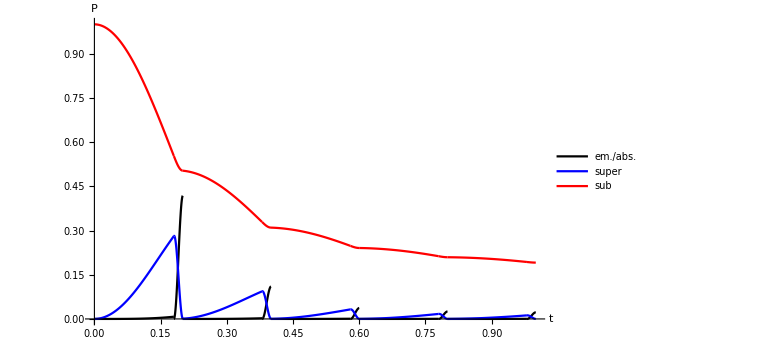

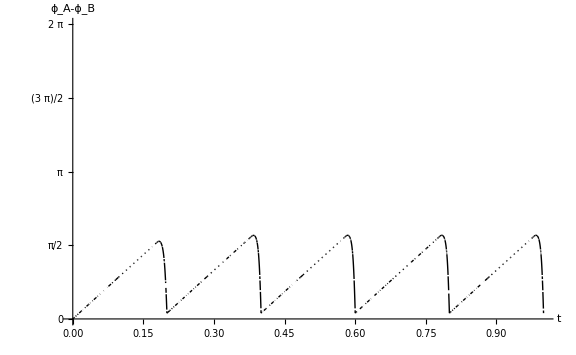

```mathematica
Print[Show[pltP,PlotRange-> All]];
Print[Show[pltAsync,PlotRange->{0,2π}]];
(*Print[Show[pltClockPhases,PlotRange-> All]];
Print[Show[pltPClock,PlotRange-> All]];*)
(*Do[
Print[e1[m]];
Print[g1[m]];
Print[e2[m]];
Print[g2[m]];
Print[Ωal[m]];
,{m,1,M}];*)
NotebookSave@EvaluationNotebook[];
Quit[];
```

### Compiled Results

#### Free evolution [ measure =0, ShineFullTime = 0 ]

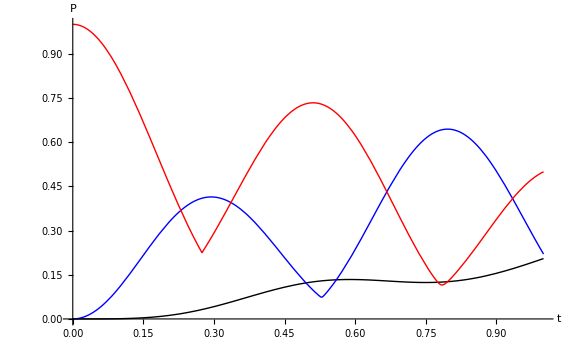

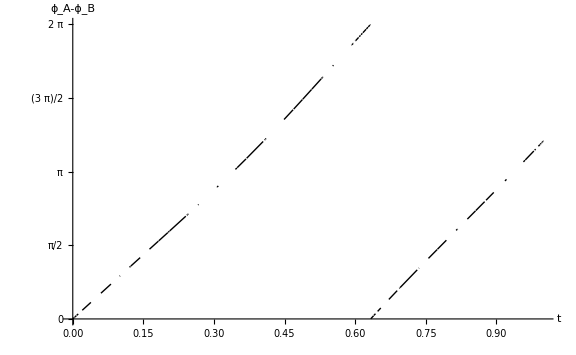

#### interval = 2 10^-1

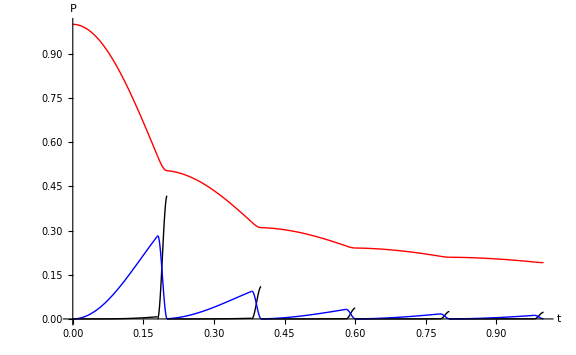

-Graphics-

#### interval = 5 10^-2

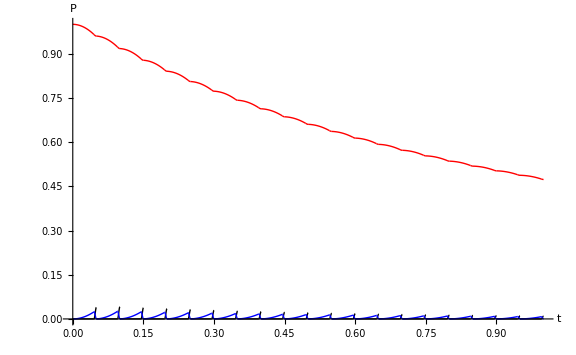

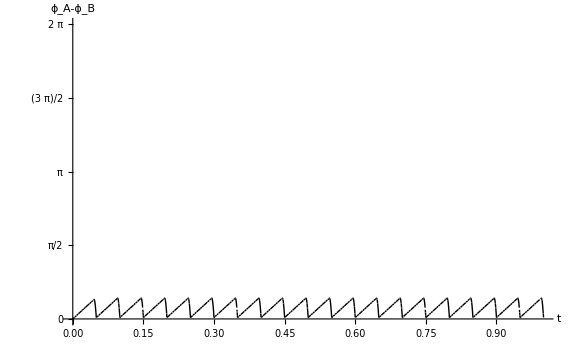

#### interval=10^-3

-Graphics-

-Graphics-